```mathematica
Exp[-Integrate[Exp[ t],{t,0,T}]]
```

ⅇ^(1-ⅇ^T)

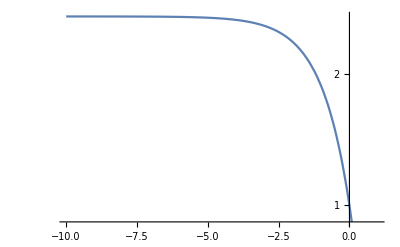

```mathematica
LogPlot[ⅇ^(-(-1+ⅇ^T)),{T,-10,1}]
```

```mathematica
1-Exp[-Integrate[10^(.088t),{t,T,T+1}]]
```

1-ⅇ^(-1.10852 ⅇ^(0.202627 T))

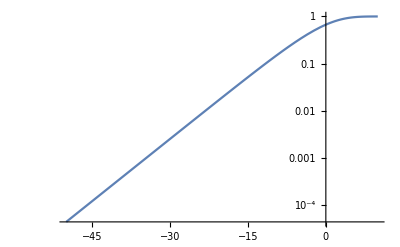

```mathematica
LogPlot[1-ⅇ^(-1.1085179078055905 ⅇ^(0.20262748818347603 T)),{T,-50,10}]
```

```mathematica
Table[{T,1-ⅇ^(-1.1085179078055905 ⅇ^(0.20262748818347603 (T-94)))},{T,40,100,5}]
```

{{40,0.0000196218},{45,0.0000540419},{50,0.000148837},{55,0.000409877},{60,0.00112849},{65,0.00310504},{70,0.00852872},{75,0.0233147},{80,0.0629086},{85,0.163856},{90,0.389136},{95,0.742699},{100,0.97622}}

```mathematica
{#[[1]],Log10[#[[2]]]}&/@%37
```

{{40,-4.70726},{45,-4.26727},{50,-3.82729},{55,-3.38735},{60,-2.9475},{65,-2.50793},{70,-2.06912},{75,-1.63237},{80,-1.20129},{85,-0.785537},{90,-0.409898},{95,-0.129187},{100,-0.0104525}}

```mathematica
(Log10[0.000054041945865890284]-Log10[0.00001962178228087641])/5
```

0.0879985

```mathematica
(Log10[0.7426990807631515]-Log10[0.38913648371162723])/5
```

0.0561422

```mathematica
%%-%
```

0.0318563

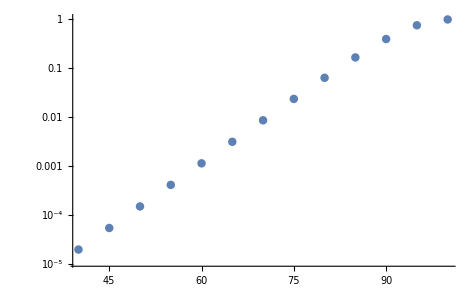

```mathematica
ListLogPlot[%]
```

```mathematica
(* compare https://journals.plos.org/plosbiology/article?id=10.1371/journal.pbio.2006776 Fig 1 *)
```

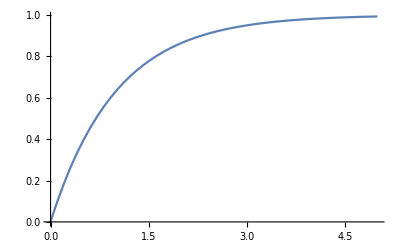

```mathematica
Plot[1-Exp[-q],{q,0,5}]
```

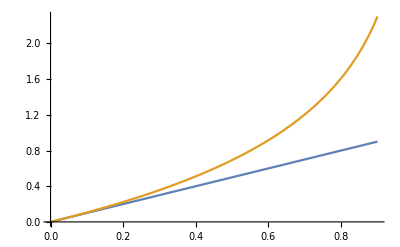

```mathematica
Plot[{q,-Log[1-q]},{q,0,.9}]
```